## Initialization

### Overall Project

```mathematica
startDate = DateList[{2012, 6, 15}]
```

{2012,6,15,0,0,0.}

```mathematica
endDate = DateList[{2013,10,8}]
```

{2013,10,8,0,0,0.}

```mathematica
projectDurationDays = DateDifference[startDate,endDate]
```

480 days

```mathematica
projectDurationMonths = DateDifference[startDate,endDate, "Month"]
```

15.7667 mo

```mathematica
Head[projectDurationMonths]
```

Quantity

```mathematica
(* Percentage that design overlaps with requirements, coding overlaps with desgin, etc. Depends on type of project. Can be individually set for any phase as a function of any other. *)
```

```mathematica
percentageOverlap = 0.663;
```

### Requirements

```mathematica
requirementsStartDate = startDate;
```

```mathematica
(* Requirements duration is specified in months *)
```

```mathematica
requirementsDuration = 1.91;
```

```mathematica
requirementsXStagger = 0;
```

```mathematica
requirementsEndDate = DatePlus[requirementsStartDate, {requirementsDuration, "Month"}]
```

{2012,8,12,5,2,24}

```mathematica
(* Number of days that the Requirements phase takes *)
```

```mathematica
requirementsNDays = DateDifference[requirementsStartDate, requirementsEndDate]
```

58.21 days

### Design

```mathematica
(* The design phase starts when the requirements phase is 66.3% complete *)
```

```mathematica
designStartDate = DatePlus[requirementsStartDate, {requirementsDuration * percentageOverlap, "Month"}]
```

{2012,7,23,6,8,58.272}

```mathematica
(* If the Requirements chart starts at x = 0, then the x value at which the Design phase starts is percentageOverlap * requirementsNDays *)
designXStagger = requirementsXStagger + (percentageOverlap * requirementsNDays)
```

38.5932 days

```mathematica
(* Design duration is specified in months *)
```

```mathematica
designDuration = 2.42;
```

```mathematica
designEndDate = DatePlus[designStartDate, {designDuration, "Month"}]
```

{2012,10,5,20,32,58.272}

```mathematica
(* Number of days that the Design phase takes *)
```

```mathematica
designNDays = DateDifference[designStartDate, designEndDate]
```

74.6 days

### Coding

```mathematica
(* The coding phase starts when the design phase is 66.3% complete *)
```

```mathematica
codingStartDate = DatePlus[designStartDate, {designDuration * percentageOverlap, "Month"}]
```

{2012,9,10,23,52,3.936}

```mathematica
(* If the desgin chart starts at x = 0, then the x value at which the coding phase starts is percentageOverlap * designNDays *)
codingXStagger = designXStagger + (percentageOverlap * designNDays)
```

88.053 days

```mathematica
(* Coding duration is specified in months *)
```

```mathematica
codingDuration = 6.8;
```

```mathematica
codingEndDate = DatePlus[codingStartDate, {codingDuration, "Month"}]
```

{2013,4,4,19,4,3.936}

```mathematica
(* Number of days that the Coding phase takes *)
```

```mathematica
codingNDays = DateDifference[codingStartDate, codingEndDate]
```

205.8 days

### Testing

```mathematica
(* The Testing phase starts when the Coding phase is 66.3% complete *)
```

```mathematica
testingStartDate = DatePlus[codingStartDate, {codingDuration * percentageOverlap, "Month"}]
```

{2013,1,26,18,7,2.496}

```mathematica
(* If the coding chart starts at x = 0, then the x value at which the testing phase starts is percentageOverlap * codingNDays *)
testingXStagger = codingXStagger + (percentageOverlap * codingNDays)
```

224.498 days

```mathematica
(* Coding duration is specified in months *)
```

```mathematica
testingDuration = 4.58;
```

```mathematica
testingEndDate = DatePlus[testingStartDate, {testingDuration, "Month"}]
```

{2013,6,13,17,38,14.496}

```mathematica
(* Number of days that the Testing phase takes *)
```

```mathematica
testingNDays = DateDifference[testingStartDate, testingEndDate]
```

137.98 days

### Documentation

```mathematica
(* The Documentation phase starts when the Coding phase is 66.3% complete *)
```

```mathematica
documentationStartDate = DatePlus[codingStartDate, {codingDuration * percentageOverlap, "Month"}]
```

{2013,1,26,18,7,2.496}

```mathematica
(* If the coding chart starts at x = 0, then the x value at which the documentation phase starts is percentageOverlap * codingNDays *)
documentationXStagger = codingXStagger + (percentageOverlap * codingNDays)
```

224.498 days

```mathematica
(* Documentation duration is specified in months *)
```

```mathematica
documentationDuration = 2.42;
```

```mathematica
documentationEndDate = DatePlus[documentationStartDate, {documentationDuration, "Month"}]
```

{2013,4,8,18,35,50.496}

```mathematica
(* Number of days that the Documentation phase takes *)
```

```mathematica
documentationNDays = DateDifference[documentationStartDate, documentationEndDate]
```

72.02 days

### QA

```mathematica
(* The QA phase starts when the Coding phase is 66.3% complete *)
```

```mathematica
qaStartDate = DatePlus[codingStartDate, {codingDuration * percentageOverlap, "Month"}]
```

{2013,1,26,18,7,2.496}

```mathematica
(* If the coding chart starts at x = 0, then the x value at which the QA phase starts is percentageOverlap * codingNDays *)
qaXStagger = codingXStagger + (percentageOverlap * codingNDays)
```

224.498 days

```mathematica
(* QA duration is specified in months *)
```

```mathematica
qaDuration = 3.86;
```

```mathematica
qaEndDate = DatePlus[qaStartDate, {qaDuration, "Month"}]
```

{2013,5,22,13,19,2.496}

```mathematica
(* Number of days that the QA phase takes *)
```

```mathematica
qaNDays = DateDifference[qaStartDate, qaEndDate]
```

115.8 days

### Management

```mathematica
(* The management phase runs throughout the entire duration of the project from start to finish *)
```

```mathematica
managementStartDate = startDate
```

{2012,6,15,0,0,0.}

```mathematica
(* The management phase lasts throughtout the project, hence managementXStagger = 0 *)
managementXStagger = 0;
```

```mathematica
(* Management duration is specified in months *)
```

```mathematica
managementDuration = projectDurationMonths
```

15.7667 mo

```mathematica
managementEndDate = endDate
```

{2013,10,8,0,0,0.}

```mathematica
(* Number of days that the Management phase takes *)
```

```mathematica
managementNDays = projectDurationDays
```

480 days

## Gantt Chart

### Set up a single component of the Gantt chart

```mathematica
line1 = Graphics[Line[{{0,30}, {QuantityMagnitude[requirementsNDays],30}}]];
```

```mathematica
point11 = Graphics[{PointSize[Large],Point[{0,30}]}];
```

```mathematica
point12 = Graphics[{PointSize[Large],Point[{QuantityMagnitude[requirementsNDays],30}]}];
```

```mathematica
text11 = Graphics[Text[Style["Requirements Start\n " <> DateString[requirementsStartDate,{"MonthNameShort"," ","DayShort",", ","Year"}],Medium, Blue, FontFamily-> "Courier"], {0 - 30,35}]];
```

```mathematica
text12 = Graphics[Text[Style["Requirements End\n " <> DateString[requirementsEndDate,{"MonthNameShort"," ","DayShort",", ","Year"}],Medium, Blue, FontFamily-> "Courier"], {QuantityMagnitude[requirementsNDays] + 30,35}]];
```

```mathematica
text13 = Graphics[Text[Style[ToString[requirementsNDays], Medium, FontFamily->"Arial"],{QuantityMagnitude[requirementsNDays]/2,35} ]];
```

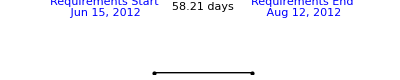

```mathematica
Show[text11, point11, line1, point12, text12, text13]
```

```mathematica
reqChart = {text11, point11, line1, point12, text12, text13};
```

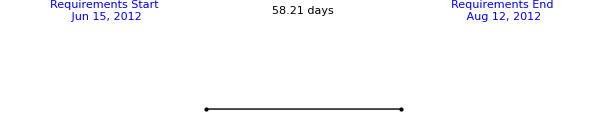

```mathematica
Show[reqChart, ImageSize-> 600]
```

### Function to generate a single component of the Gantt chart

```mathematica
(* Build a function to generate the components of a single timeline *)
```

```mathematica
gantt[phaseName_, xAxisValStagger_, yAxisVal_, phaseStartDate_, phaseEndDate_]:= Module[{nPhaseDays = DateDifference[phaseStartDate, phaseEndDate],line1, point1, point2, text1XShift = -30,text1YShift = 10, text1, text2XShift = 30,text2YShift = 10, text2, text3YShift = 5,text3, out},
(* Note that gantt only outputs the values for a single phase of the complete Gantt chart. *)
(* To create the entire Gantt chart, use gantt repeately by providing the right inputs for each phase of the project *)
(* Then use Show to display all of the phases together to form the complete Gantt chart for the project. *)
(* xAxisValStagger is the stagger in the start of the gantt line from the point x=0 *)
(* The value of xAxisValStagger will be 0 for the first phase and then positive for every other phase displayed in the Gantt chart *)
(* phaseStartData and phaseEndDate are given as a DateList[{year, month, day}] *)
(* nPhaseDays is the duration of the phase in days *)
(* text1XShift and text2XShift shift the text to the side of the Point or Line -- left or right depending on the sign of the shift *)
(* text1YShift, text2Yshift, and text3YShift specify the distance the text is placed above the Point or Line objects. Note: It is best to set text1YShift and text2YShift to the same magnitude. *)
line1 = Graphics[Line[{{xAxisValStagger,yAxisVal}, {xAxisValStagger + QuantityMagnitude[nPhaseDays],yAxisVal}}]];
point1 = Graphics[{PointSize[Large],Point[{xAxisValStagger,yAxisVal}]}];
point2 = Graphics[{PointSize[Large],Point[{xAxisValStagger + QuantityMagnitude[nPhaseDays],yAxisVal}]}];
text1 = Graphics[Text[Style[phaseName <> " Start\n " <> DateString[phaseStartDate,{"MonthNameShort"," ","DayShort",", ","Year"}],10, Bold,Blue, FontFamily-> "Courier"], {xAxisValStagger + text1XShift,yAxisVal + text1YShift}]];
text2 = Graphics[Text[Style[phaseName <> " End\n " <> DateString[phaseEndDate,{"MonthNameShort"," ","DayShort",", ","Year"}],10, Bold,Blue, FontFamily-> "Courier"], {xAxisValStagger + QuantityMagnitude[nPhaseDays] + text2XShift,yAxisVal + text2YShift}]];
text3 = Graphics[Text[Style[ToString[nPhaseDays], 10, Bold, FontFamily->"Arial"],{xAxisValStagger + QuantityMagnitude[nPhaseDays]/2,yAxisVal + text3YShift} ]];
out = {line1, point1, point2, text1, text2, text3}
]
```

### Generate the Gantt chart

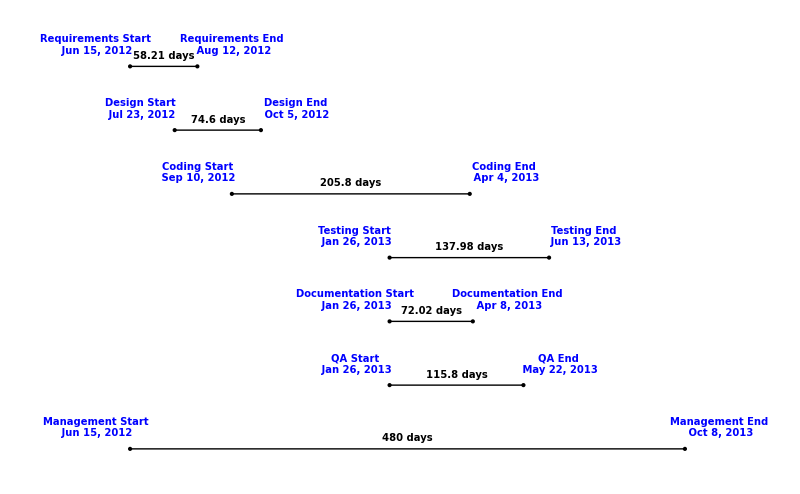

```mathematica
gc = Show[gantt["Requirements", 0, 200, requirementsStartDate,requirementsEndDate], gantt["Design", QuantityMagnitude[designXStagger], 170, designStartDate,designEndDate],gantt["Coding", QuantityMagnitude[codingXStagger], 140, codingStartDate,codingEndDate],gantt["Testing", QuantityMagnitude[testingXStagger], 110, testingStartDate,testingEndDate],
gantt["Documentation", QuantityMagnitude[documentationXStagger], 80, documentationStartDate,documentationEndDate],gantt["QA", QuantityMagnitude[qaXStagger], 50, qaStartDate,qaEndDate],gantt["Management", QuantityMagnitude[managementXStagger], 20, managementStartDate,managementEndDate], ImageSize-> 800, AspectRatio-> 1/GoldenRatio]
```

## Animation

```mathematica
ganttList = {gantt["Requirements", 0, 200, requirementsStartDate,requirementsEndDate], gantt["Design", QuantityMagnitude[designXStagger], 170, designStartDate,designEndDate],gantt["Coding", QuantityMagnitude[codingXStagger], 140, codingStartDate,codingEndDate],gantt["Testing", QuantityMagnitude[testingXStagger], 110, testingStartDate,testingEndDate],
gantt["Documentation", QuantityMagnitude[documentationXStagger], 80, documentationStartDate,documentationEndDate],gantt["QA", QuantityMagnitude[qaXStagger], 50, qaStartDate,qaEndDate],gantt["Management", QuantityMagnitude[managementXStagger], 20, managementStartDate,managementEndDate]};
```

```mathematica
Export["ganttanimation.avi", ganttList]
```

ganttanimation.avi

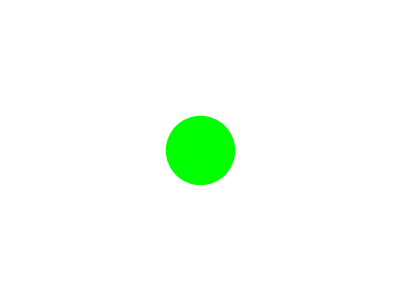

```mathematica
Graphics[{Green,Dashed, PointSize[1/2],Point[{0,0}]}]
```

```mathematica
Animate[Plot[Table[{i,30}, {i,0,60}], {x, 0, 60}], {x,0,60}]
```

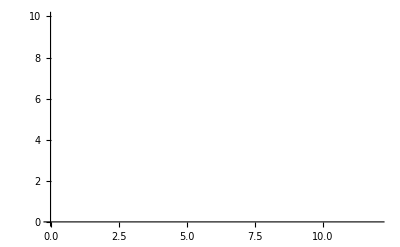
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
t = Table[ListLinePlot[{{i,i+1}}, PlotRange->{{0,12},{0,10}}], {i, 1,10}]
```

```mathematica
Head[%[[1]]]
```

Graphics

```mathematica
ListAnimate[t, {0,1,100}]
```